```mathematica
tF = {{F11,F12,F13},{F21,F22,F23},{F31,F32,F33}};
tC = Transpose[tF].tF;
```

```mathematica
ϕ=(20.61)/180 * Pi;
n1 = {Cos[ϕ],0, Sin[ϕ]};
n2 = {Cos[ϕ],0, -Sin[ϕ]};
A1 = KroneckerProduct[n1,n1];
A2 = KroneckerProduct[n2,n2];
I1=Tr[tC];
I4 = Tr[tC.A1];
I6 = Tr[tC.A2];
μ ;k1;k2;pp;ρ;
W = μ(I1-3)+k1/(2k2)(Exp[k2((1-pp)(I1-3)^2 +pp (I4-1)^2)]-1)+k1/(2k2)(Exp[k2((1-pp)(I1-3)^2 +pp (I6-1)^2)]-1);
dWdF = D[W,{tF}];
P = dWdF - ρ Transpose[Inverse[tF]];
sigma =1.0/Det[tF] P.Transpose[tF]; 
Dimensions[sigma]
```

{3,3}

初始化参数

```mathematica
F12 = 0.;
F13 =0.;
F21 =0.;
F23 =0.;
F31 =0.;
F32 =0.;
{μ ,k1,k2,pp} = {1.27,21.6, 8.21, 0.25};
```

单轴拉伸x

```mathematica
F11 =.;
F22=.;
F33=.;
F22 =1/(F11 F33);
(*P[[3,1]]/.{F11->0.5, F33->2.0}*)
solutionUniaxialX= Solve[{P[[2,2]]==0,P[[3,3]]==0, F22>0,F33>0},{F33,ρ}, Reals];
(*tmpF11 = 1.2214027581601699;
F33AndRho = solutionUniaxialX/.{F11->tmpF11}*)
(*P[[2,2]]/.{F11->1.25,ρ->18.559786129879054, F33->0.8727739174030389}*)
(*F33AndRho[[1,1,2]]
F33AndRho[[1,2,2]]*)
(*P/.{F11->tmpF11, F33->F33AndRho[[1,1,2]], ρ->F33AndRho[[1,2,2]]}//MatrixForm
sigma/.{F11->tmpF11, F33->F33AndRho[[1,1,2]], ρ->F33AndRho[[1,2,2]]}//MatrixForm*)
```

Solve::inex: Solve 无法求解具有不精确系数的系统或通过将系统中出现的不精确数直接合理化处理得到的系统. 由于 Solve 所用的许多方法需要精确输入，为 Solve 提供一个精确版本的系统可能会有帮助.

```mathematica
F11s = Table[f11,{f11,0.8,1.2, 0.002}];
n = Dimensions[F11s][[1]];
F33AndRhos = Table[solutionUniaxialX/.{F11->f11},{f11,F11s}];
(*F33AndRhos;
F33AndRhos[[1,1,1,2]];
F33AndRhos[[1,1,2,2]];*)
sigmas = Table[sigma/.{F11->F11s[[i]], F33->F33AndRhos[[i,1,1,2]], ρ->F33AndRhos[[i,1,2,2]]},{i,n}];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

General::stop: 在本次计算中，Solve::ratnz 的进一步输出将被抑制.

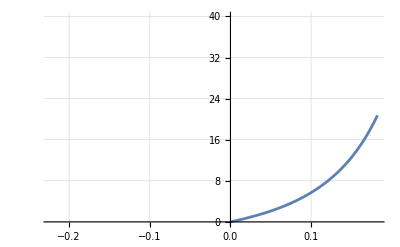

```mathematica
loglam1 = Log[F11s];
sig11 = Table[sigmas[[i,1,1]],{i,n}];
myplot2 = Table[{loglam1[[i]],sig11[[i]]},{i,n}];
ListLinePlot[myplot2, DataRange->0.25 ,PlotRange->40, GridLines->Automatic]
```

```mathematica
tFs = Table[tF/.{F11->F11s[[i]],F33->F33AndRhos[[i,1,1,2]]},{i,n}];
Dimensions[tFs]
Export["/Users/refantasy/code/BioConstitutiveNN/Data/OrthotropicHGO/out1.txt",tFs]
```

{201,3,3}

/Users/refantasy/code/BioConstitutiveNN/Data/OrthotropicHGO/out1.txt

单轴拉伸 y

```mathematica
F11 =.;
F22=.;
F33=.;
F11 =1/(F22 F33);
solutionUniaxialY= Solve[{P[[1,1]]==0,P[[3,3]]==0, F22>0,F33>0},{F33,ρ}, Reals];
```

Solve::inex: Solve 无法求解具有不精确系数的系统或通过将系统中出现的不精确数直接合理化处理得到的系统. 由于 Solve 所用的许多方法需要精确输入，为 Solve 提供一个精确版本的系统可能会有帮助.

```mathematica
F22s = Table[f22,{f22,0.8,1.2, 0.002}];
n = Dimensions[F22s][[1]];
F33AndRhos = Table[solutionUniaxialY/.{F22->f22},{f22,F22s}];
sigmas2 = Table[sigma/.{F22->F22s[[i]], F33->F33AndRhos[[i,1,1,2]], ρ->F33AndRhos[[i,1,2,2]]},{i,n}];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

General::stop: 在本次计算中，Solve::ratnz 的进一步输出将被抑制.

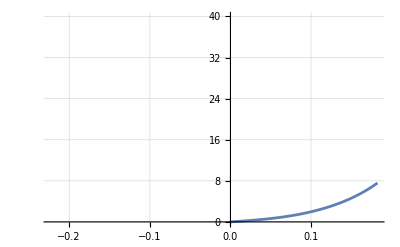

```mathematica
loglam2 = Log[F22s];
sig22 = Table[sigmas2[[i,2,2]],{i,n}];
myplot3 = Table[{loglam2[[i]],sig22[[i]]},{i,n}];
ListLinePlot[myplot3, DataRange->0.25 ,PlotRange->40, GridLines->Automatic]
```

```mathematica
tFs = Table[tF/.{F22->F22s[[i]],F33->F33AndRhos[[i,1,1,2]]},{i,n}];
Dimensions[tFs]
Export["/Users/refantasy/code/BioConstitutiveNN/Data/OrthotropicHGO/out2.txt",tFs]
```

{201,3,3}

/Users/refantasy/Downloads/out2.txt

```mathematica
(*tPs = Table[P/.{F22->F22s[[i]],F33->F33AndRhos[[i,1,1,2]],ρ->F33AndRhos[[i,1,2,2]]},{i,n}];
Export["/Users/refantasy/Downloads/P2.txt",tPs]
tPs[[1]]*)
```

单轴拉伸 z

```mathematica
F11 =.;
F22=.;
F33=.;
F11 =1/(F22 F33);
solutionUniaxialZ= Solve[{P[[1,1]]==0,P[[2,2]]==0, F22>0,F33>0},{F22,ρ}, Reals];
(*tmpF33 = 1.2214027581601699;
F22AndRho = solutionUniaxialZ/.{F33->tmpF33}*)
(*P[[2,2]]/.{F11->1.25,ρ->18.559786129879054, F33->0.8727739174030389}*)
(*F33AndRho[[1,1,2]]
F33AndRho[[1,2,2]]*)
(*P/.{F11->tmpF11, F33->F33AndRho[[1,1,2]], ρ->F33AndRho[[1,2,2]]}//MatrixForm
sigma/.{F11->tmpF11, F33->F33AndRho[[1,1,2]], ρ->F33AndRho[[1,2,2]]}//MatrixForm*)
```

Solve::inex: Solve 无法求解具有不精确系数的系统或通过将系统中出现的不精确数直接合理化处理得到的系统. 由于 Solve 所用的许多方法需要精确输入，为 Solve 提供一个精确版本的系统可能会有帮助.

```mathematica
F33s = Table[f33,{f33,0.8,1.2, 0.002}];
n = Dimensions[F33s][[1]];
F22AndRhos = Table[solutionUniaxialZ/.{F33->f33},{f33,F33s}];
sigmas3 = Table[sigma/.{F33->F33s[[i]], F22->F22AndRhos[[i,1,1,2]], ρ->F22AndRhos[[i,1,2,2]]},{i,n}];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

General::stop: 在本次计算中，Solve::ratnz 的进一步输出将被抑制.

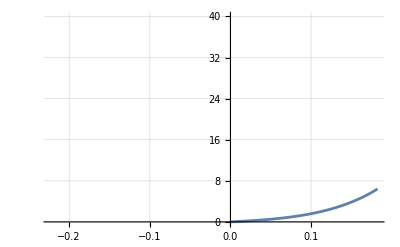

```mathematica
loglam3 = Log[F33s];
sig33 = Table[sigmas3[[i,3,3]],{i,n}];
myplot4 = Table[{loglam3[[i]],sig33[[i]]},{i,n}];
ListLinePlot[myplot4, DataRange->0.25 ,PlotRange->40, GridLines->Automatic]
```

```mathematica
tFs = Table[tF/.{F33->F33s[[i]],F22->F22AndRhos[[i,1,1,2]]},{i,n}];
Dimensions[tFs]
Export["/Users/refantasy/code/BioConstitutiveNN/Data/OrthotropicHGO/out3.txt",tFs]
```

{201,3,3}

/Users/refantasy/Downloads/out3.txt